## Metric

```mathematica
Quit
```

```mathematica
coord={t,x1,x2,x3};
dim=Length[coord];
metricsign=-1;
metric=({{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})+ϵ ({{h00[t,x3], h01[t,x3], h02[t,x3], h03[t,x3]}, {h01[t,x3], h11[t,x3], h12[t,x3], h13[t,x3]}, {h02[t,x3], h12[t,x3], h22[t,x3], h23[t,x3]}, {h03[t,x3], h13[t,x3], h23[t,x3], h33[t,x3]}})+O[ϵ]^2;
gμν=metric;
gμνUU=Inverse[metric];
g=Det[metric];

SetDirectory[NotebookDirectory[]];
Quiet[Get["diffgeo.m"]]
```

## Velocity and vorticity

```mathematica
speedU=({{1}, {0}, {0}, {0}})+ϵ({{1/2 uT[t,x3]}, {u1[t,x3]}, {u2[t,x3]}, {u3[t,x3]}})+O[ϵ]^2;
uμU=speedU⟦;;,1⟧/.Solve[0==Coefficient[∑_(i=1)^dim speedU⟦i⟧(gμν.speedU)⟦i⟧,ϵ],uT[t,x3]]⟦1⟧;
uμ=lower[uμU];

ωμU=Table[∑_(j=1)^dim ∑_(k=1)^dim ∑_(l=1)^dim Signature[{i,j,k,l}]/g uμ⟦j⟧covariant[uμ]⟦k,l⟧,{i,dim}];
ωμ=lower[ωμU];
```

## Maxwell

```mathematica
Aμ=({{μ}, {0}, {0}, {0}})+1/2({{0}, {x2 B}, {-x2 B}, {0}})+ϵ({{1/2 A0[t,x3]}, {A1[t,x3]}, {A2[t,x3]}, {A3[t,x3]}})+O[ϵ]^2;

Fμν=Table[D[Aμ⟦j⟧,coord⟦i⟧]-D[Aμ⟦i⟧,coord⟦j⟧],{i,1,dim},{j,1,dim}]⟦;;,;;,1⟧;
FμνUU=raise[Fμν];


Eμ=Fμν.uμU;
EμU=raise[Eμ];

BμU=Table[∑_(j=1)^dim ∑_(k=1)^dim ∑_(l=1)^dim Signature[{i,j,k,l}]/g 1/2 uμ⟦j⟧Fμν⟦k,l⟧,{i,dim}];
Bμ=lower[BμU];
```

## Expansions

```mathematica
T=T0+ϵ T1[t,x3]+O[ϵ]^2;
μ=μ0+ϵ μ1[t,x3]+O[ϵ]^2;

P=P0+ϵ (T1[t,x3]PT+ μ1[t,x3]Pμ)+O[ϵ]^2;
ee=e0+ϵ (T1[t,x3]eT+ μ1[t,x3]eμ)+O[ϵ]^2;
n=n0 + ϵ(T1[t,x3] nT + μ1[t,x3] nμ)+O[ϵ]^2;
```

## Derivative order correction

```mathematica
Pμν=gμν+Table[uμ⟦i⟧uμ⟦j⟧,{i,dim},{j,dim}];
PμνUU=raise[Pμν];
νν=-σ T PμνUU.Table[D[μ/T,coord⟦i⟧],{i,dim}]+σ EμU + ξB BμU +ξv ωμU;

t1=Table[∑_(i=1)^dim ∑_(j=1)^dim PμνUU⟦α,i⟧PμνUU⟦α,i⟧covariant[uμ]⟦i,j⟧,{α,dim},{β,dim}];
t2=Table[∑_(i=1)^dim ∑_(j=1)^dim PμνUU⟦α,i⟧PμνUU⟦α,i⟧covariant[uμ]⟦j,i⟧,{α,dim},{β,dim}];
t3=Table[∑_(i=1)^dim ∑_(j=1)^dim PμνUU⟦α,i⟧PμνUU⟦α,i⟧gμν⟦i,j⟧Tr[covariant[uμU,{up}]],{α,dim},{β,dim}];

q1PμU=ξv BμU + ξ3 ωμU;
τμνUU=-η (t1+t2-2/3 t3)-ζ PμνUU Tr[covariant[uμU,{up}]]+(Table[uμU⟦i⟧q1PμU⟦j⟧+uμU⟦j⟧q1PμU⟦i⟧,{i,dim},{j,dim}]);
```

## Totals

```mathematica
Tμν0UU=ee Table[uμU⟦i⟧ uμU⟦j⟧,{i,dim},{j,dim}]+P PμνUU ;

Jμ0U= n uμU ;

TμνUU=Tμν0UU+τμνUU;
JμU=Jμ0U+νν;

Tμν=lower[TμνUU];
Jμ=lower[JμU];

Tμν/.ϵ->0//MatrixForm
Jμ/.ϵ->0//MatrixForm
```

(e0 | 0 | 0 | -(B ξv)/2
0 | P0 | 0 | 0
0 | 0 | P0 | 0
-(B ξv)/2 | 0 | 0 | P0)

```mathematica
1
```

(-n0
0
0
(B ξB)/2)

## Equation of motion

```mathematica
maxwell=∑_(j=1)^dim D[√-g FμνUU⟦;;,j⟧,coord⟦j⟧]+γ/8 Table[∑_(pp=1)^dim ∑_(qq=1)^dim ∑_(rr=1)^dim ∑_(ss=1)^dim LeviCivitaTensor[5]⟦pp,qq,rr,ss,mm⟧Fμν⟦pp,qq⟧Fμν⟦rr,ss⟧,{mm,dim}];
einstein=RicciTensor-1/2 metric (RicciScalar+12+Tr[Fμν.FμνUU])+2Fμν.raise[Fμν,{1}];
```

## Fourier modes

```mathematica
ruleFR={Derivative[aa_,bb_,cc_][func_][v,x3,r]->(-ⅈ ω)^aa(ⅈ k)^bb D[func[r],{r,cc}],
func_[v,x3,r]->func[r]};

maxFR=Coefficient[maxwell,ϵ]/.ruleFR//Simplify;
ensFR=Coefficient[einstein,ϵ]/.ruleFR//Simplify;
```

## Spin 2

```mathematica
eqXY=2 r^6 ensFR⟦2,3⟧
```

(-8 q^2+4 m r^2+r^4 (k^2+4 r^2+ⅈ r ω)) h12[r]-r ((-5 q^2+3 m r^2+r^6+2 ⅈ r^5 ω) h12'[r]+r (q^2-m r^2+r^6) h12''[r])

```mathematica
eqXY/.r->1/z/.ff_[1/z]->ff[z]//Simplify;
%/.ff_[zI_]->zI^-α ff[zI]
%/.fff_[z]->(1+O[z])//Simplify
```

(z^(2-α) (4+k^2 z^2+4 m z^4-8 q^2 z^6+ⅈ z ω) h12[z]+z^(1-α) (-1-3 m z^4+5 q^2 z^6-2 ⅈ z ω) h12'[z]+z^-α (-1+m z^4-q^2 z^6) h12''[z])/z^8

z^-α (-1/z^8+1/O[z]^7)

### Horizon expansion

```mathematica
eqXY/.r->rH+δr/.h12->((#-rH)^γ g[#-rH]&);
%/.g->(1+O[#]&)//Simplify;
Solve[Normal[%] δr^-γ==0,γ]
```

{{γ→0},{γ→1}}

### Boundary expansion

```mathematica
eqXY/.r->1/z/.h12->(#^-α h12[1/#]&)//Simplify
%/.h12->(1+O[#]&)//Simplify
Solve[Normal[%] δr^-α==0,α]
```

(1/z)^(6-α) ((4+k^2 z^2-8 q^2 z^6-6 q^2 z^6 α-α^2-q^2 z^6 α^2+m z^4 (2+α)^2+ⅈ z ω+2 ⅈ z α ω) h12[z]-z ((1+2 α-m z^4 (5+2 α)+q^2 z^6 (7+2 α)-2 ⅈ z ω) h12'[z]+z (1-m z^4+q^2 z^6) h12''[z]))

(1/z)^-α ((4-α^2)/z^6+1/O[z]^5)

{{α→-2},{α→2}}

### Z-coordiante

```mathematica
ruleScale={q->q rH^3,m->rH^4(1+q^2),ω->ω rH,k->k rH,h12-> Function[z,h12[z]/rH^6]};

(2 rH^8)/z^3 eqXY/.r->rH/z/.h12->(#^-2 h12[rH/#]&)//PowerExpand//Simplify;

zCoordXY=z^6/(2 rH^6)%/.ruleScale//Simplify
```

(k^2 z+16 (1+q^2) z^3-24 q^2 z^5+5 ⅈ ω) h12[z]+(-5+9 (1+q^2) z^4-11 q^2 z^6+2 ⅈ z ω) h12'[z]+z (-1+(1+q^2) z^4-q^2 z^6) h12''[z]

### Spectral code

```mathematica
sub[MM_]:=h12:>Function[z,∑_(i=0)^MM c[i] cheby[i,2z-1]];

grid[MM_,prec_]:=Table[1/2(1-Cos[(i Pi)/MM])//N[#,prec]&,{i,0,MM}];

cof[MM_]:=Table[c[i],{i,0,MM}];

geneigs[mtx_]:=Eigensystem[{mtx/.ω->0,Coefficient[mtx,ω]}]//Reverse;

QNM[MM_,kk_,qq_,prec_:MachinePrecision]:=geneigs[(Coefficient[#,cof[MM]]&/@((zCoordXY/.{k->kk,q->qq,sub[MM],z->#})&/@grid[MM,prec]))/.chebysub];

chebysub={Derivative[0,m_][cheby][n_,z_?NumberQ]->n 2^(m-1)(m-1)!GegenbauerC[n-m,m,z],
cheby[n_,z_?NumberQ]->ChebyshevT[n,z]};
```

### Results

```mathematica
QNM20000016=QNM[20,0,0,16];
```

```mathematica
QNM20000016⟦1⟧
```

{{0.053427499113-0.39720518314 ⅈ,-0.20075582535+0.76980775469 ⅈ,0.3730250682-0.6269749318 ⅈ,-0.49354927567+0.3781126789 ⅈ,0.49004273083-0.100522046 ⅈ,-0.3666803191-0.11663522949 ⅈ,0.18359598488+0.21849811564 ⅈ,-0.016964898618-0.20456184891 ⅈ,-0.079402080397+0.11972024153 ⅈ,0.094633339879-0.025486880435 ⅈ,-0.056732162304-0.032109849712 ⅈ,0.0091600876429+0.041216734563 ⅈ,0.016709810114-0.020631759865 ⅈ,-0.016079711017-0.001215163757 ⅈ,0.0041697486128+0.0084092853146 ⅈ,0.0031206037083-0.0041284635641 ⅈ,-0.0025688156404-0.00067878529235 ⅈ,0.000071240308954+0.0012377312239 ⅈ,0.00048139083273-0.0001585276235 ⅈ,-0.000076163961327-0.00014485798893 ⅈ,-0.00003363811418+0.000029933456299 ⅈ},{0.14588553391-0.39160444174 ⅈ,-0.19331585334+0.80668414666 ⅈ,-0.035278948994-0.75988433237 ⅈ,0.26833717161+0.59014559244 ⅈ,-0.40141098763-0.3330807752 ⅈ,0.39456152477+0.072755635975 ⅈ,-0.27616605343+0.11083937121 ⅈ,0.11604682617-0.17983728983 ⅈ,0.014254741942+0.14911232523 ⅈ,-0.074534659331-0.069909992426 ⅈ,0.067951556847-0.0016804318443 ⅈ,-0.028663712753+0.033415731037 ⅈ,-0.0052402318545-0.027182880078 ⅈ,0.01538765484+0.0067774987147 ⅈ,-0.0079645928386+0.0056879398829 ⅈ,-0.00084339205384-0.0053298295852 ⅈ,0.002696226648+0.00063692611021 ⅈ,-0.00067326714861+0.001103553411 ⅈ,-0.0003649712721-0.00038218932875 ⅈ,0.00014118627203-0.000095851172183 ⅈ,0.000016244602493+0.000044051029353 ⅈ},{0.10223500109-0.37878671346 ⅈ,-0.30260862399+0.69739137601 ⅈ,0.43250849163-0.49244787322 ⅈ,-0.4653129467+0.21937425972 ⅈ,0.37535627204+0.015497413157 ⅈ,-0.21582897927-0.14290936803 ⅈ,0.063668151928+0.15728405467 ⅈ,0.028665366672-0.1023293886 ⅈ,-0.053137029499+0.035073782022 ⅈ,0.035810572393+0.0068011729343 ⅈ,-0.010476391959-0.01688887254 ⅈ,-0.0033075384181+0.0097170995605 ⅈ,0.0047513060107-0.0015109714846 ⅈ,-0.0017705447305-0.0014032065781 ⅈ,-0.00010000840224+0.00094369956694 ⅈ,0.00033313519151-0.0001625762364 ⅈ,-0.00011845546785-0.000071266893044 ⅈ,1.4799358829×10^-6+0.000051452272004 ⅈ,0.000016365312458-9.5589455661×10^-6 ⅈ,-4.5211838903×10^-6-3.91505465×10^-6 ⅈ,-6.2274490453×10^-7+1.5161195784×10^-6 ⅈ},{-0.041461232536+0.4612959303 ⅈ,-0.050353957189-0.89601418131 ⅈ,0.27792961231+0.72207038769 ⅈ,-0.42578697314-0.43301210714 ⅈ,0.4220727612+0.13613056426 ⅈ,-0.297415779+0.070141509879 ⅈ,0.1347534672-0.14820533928 ⅈ,-0.010041625625+0.12504669394 ⅈ,-0.044530305603-0.060548785254 ⅈ,0.042441293954+0.0070920722679 ⅈ,-0.018501037667+0.014427513557 ⅈ,0.00030504142388-0.012113432192 ⅈ,0.0046454534597+0.0036139808355 ⅈ,-0.002534120061+0.00083109766477 ⅈ,0.00027463773142-0.0010860825766 ⅈ,0.00030258354494+0.00031612138072 ⅈ,-0.00016030634919+0.000030557826582 ⅈ,0.000022652273755-0.000056383995514 ⅈ,0.000014222303617+0.000017271053965 ⅈ,-6.6065589355×10^-6+2.4898534202×10^-6 ⅈ,-7.0567488522×10^-8-1.9335789589×10^-6 ⅈ},{-0.29522444531+0.23566467655 ⅈ,0.47321809652-0.52678190348 ⅈ,-0.22439359268+0.52275343323 ⅈ,-0.0059739016988-0.40783400337 ⅈ,0.12960181328+0.23449501686 ⅈ,-0.14239763544-0.080590400256 ⅈ,0.093206984263-0.0086092866157 ⅈ,-0.036724829608+0.034397806242 ⅈ,0.0027120619856-0.025278894021 ⅈ,0.0073065855449+0.0095911996328 ⅈ,-0.0053188293126-0.00064750124133 ⅈ,0.0016913419214-0.001454431872 ⅈ,-4.7493343903×10^-6+0.00087296921427 ⅈ,-0.00024675197106-0.00020943719918 ⅈ,0.00011262811682-0.000021186744086 ⅈ,-0.000017752414435+0.000034484218116 ⅈ,-5.3825556825×10^-6-0.000011292451704 ⅈ,3.8414209304×10^-6+8.2140854613×10^-7 ⅈ,-9.3077106082×10^-7+8.3223619812×10^-7 ⅈ,-9.8712361475×10^-8-3.5479196494×10^-7 ⅈ,9.7629849098×10^-8+1.176612627×10^-8 ⅈ},{0.40706249368+0.079063085167 ⅈ,-0.72829710852-0.27170289148 ⅈ,0.48420325524+0.39436084688 ⅈ,-0.20165343029-0.39976032686 ⅈ,-0.0067831759675+0.29403378774 ⅈ,0.097521391185-0.15083195366 ⅈ,-0.095046827537+0.039039552975 ⅈ,0.053222270849+0.014778674101 ⅈ,-0.015497500169-0.023210477051 ⅈ,-0.0022284678742+0.013046709482 ⅈ,0.0048445198142-0.0033355388401 ⅈ,-0.0023851238526-0.00055441860666 ⅈ,0.00044869807036+0.00084676671081 ⅈ,0.00013348812135-0.00032925286389 ⅈ,-0.00012033691108+0.000036684315552 ⅈ,0.000034810770697+0.000024513972077 ⅈ,-5.085604224×10^-7-0.000013722859617 ⅈ,-3.3189012356×10^-6+2.7531529087×10^-6 ⅈ,1.3287668054×10^-6+3.3607869049×10^-7 ⅈ,-8.4459501533×10^-8-3.9533973232×10^-7 ⅈ,-8.8984224614×10^-8+6.1109615225×10^-8 ⅈ},{0.42239337664-0.082657203967 ⅈ,-0.7210132791+0.2789867209 ⅈ,0.44212767732-0.36632976413 ⅈ,-0.16971563075+0.33269387708 ⅈ,0.00024159786078-0.21920377074 ⅈ,0.058942558934+0.10212518569 ⅈ,-0.052134980371-0.026786494489 ⅈ,0.026774050816-0.0038062040967 ⅈ,-0.0081357829959+0.0082901302553 ⅈ,0.00042001329684-0.004640303523 ⅈ,0.0010223750657+0.0014240212514 ⅈ,-0.00060800945342-0.00013036543406 ⅈ,0.00017832980703-0.00010888566247 ⅈ,-0.000016003545396+0.000064838193896 ⅈ,-0.000010825590221-0.000017311241763 ⅈ,5.9014044806×10^-6+1.1266239081×10^-6 ⅈ,-1.3451417015×10^-6+1.0436660355×10^-6 ⅈ,2.1994336218×10^-8-4.6588227594×10^-7 ⅈ,9.4277754022×10^-8+8.6335953846×10^-8 ⅈ,-3.2694785928×10^-8+9.4156441174×10^-9 ⅈ,1.3572548008×10^-9-8.5472259426×10^-9 ⅈ},{0.18030626954-0.35422463126 ⅈ,-0.4302455575+0.5697544425 ⅈ,0.43724025285-0.29996213018 ⅈ,-0.33842747493+0.066535450659 ⅈ,0.19474389765+0.055259503274 ⅈ,-0.075784411185-0.078193910565 ⅈ,0.010596208057+0.053081831748 ⅈ,0.010156157442-0.022815758769 ⅈ,-0.0094216921263+0.0051276916722 ⅈ,0.0042275136271+0.0008012964278 ⅈ,-0.0010059912455-0.0012683862898 ⅈ,-0.000038087192161+0.00057298676437 ⅈ,0.00014183534187-0.00013082533773 ⅈ,-0.00006163517552-2.1953344642×10^-6 ⅈ,0.000012635104398+0.000013995570919 ⅈ,4.9287928567×10^-7-5.5263651732×10^-6 ⅈ,-1.2673373047×10^-6+9.3054545702×10^-7 ⅈ,4.1933371999×10^-7+9.8367587895×10^-8 ⅈ,-5.2818388581×10^-8-1.0558019062×10^-7 ⅈ,-1.6636689844×10^-8+2.6654509945×10^-8 ⅈ,7.9345355559×10^-9+9.575959444×10^-10 ⅈ},{0.27626443532-0.32289942459 ⅈ,-0.50930720642+0.49069279358 ⅈ,0.39120089985-0.27045987238 ⅈ,-0.25460356314+0.10884289089 ⅈ,0.14206846799-0.025108505594 ⅈ,-0.06831607907-0.0052992849031 ⅈ,0.028177662953+0.010283325459 ⅈ,-0.0097785212313-0.0072851527749 ⅈ,0.0027043615663+0.0037558904376 ⅈ,-0.00049159964117-0.0015715823411 ⅈ,-0.000016956044885+0.00055064215742 ⅈ,0.000063845470229-0.0001615215985 ⅈ,-0.000034556273299+0.000038429326379 ⅈ,0.000012924568744-6.6218406589×10^-6 ⅈ,-3.8322921913×10^-6+3.9089860131×10^-7 ⅈ,9.2714753253×10^-7+2.6190330816×10^-7 ⅈ,-1.7953734036×10^-7-1.3746320216×10^-7 ⅈ,2.5735492328×10^-8+4.2503653999×10^-8 ⅈ,-1.809708333×10^-9-9.8844603481×10^-9 ⅈ,-2.3924576527×10^-10+1.9010742176×10^-9 ⅈ,1.5327272868×10^-10-3.3790868501×10^-10 ⅈ},{0.24818379332+0.34603336301 ⅈ,-0.46649199021-0.53350800979 ⅈ,0.36742598317+0.30351601846 ⅈ,-0.24488084011-0.13046372131 ⅈ,0.13969278736+0.037229668051 ⅈ,-0.068660846505-0.00055706814087 ⅈ,0.029013025021-0.0078549102172 ⅈ,-0.010386554749+0.0064364955803 ⅈ,0.0030215595256-0.0035184103247 ⅈ,-0.00062534498424+0.0015269968566 ⅈ,0.00003020638033-0.00055121621655 ⅈ,0.000049917351265+0.00016672945893 ⅈ,-0.000031211631096-0.000041326136837 ⅈ,0.000012337150359+7.7176351245×10^-6 ⅈ,-3.7927317908×10^-6-7.1831739771×10^-7 ⅈ,9.4808842859×10^-7-1.8212098188×10^-7 ⅈ,-1.9101510939×10^-7+1.2187337285×10^-7 ⅈ,2.9332117878×10^-8-4.023242296×10^-8 ⅈ,-2.653469773×10^-9+9.7141788176×10^-9 ⅈ,-7.5956229485×10^-11-1.9186452508×10^-9 ⅈ,1.2413274553×10^-10+3.5046775898×10^-10 ⅈ},{-0.11262883138-0.53836810124 ⅈ,0.073288440375+0.92671155963 ⅈ,0.087750782069-0.62972428315 ⅈ,-0.14976075409+0.34579906347 ⅈ,0.13145604421-0.15062795472 ⅈ,-0.084251535735+0.047413449325 ⅈ,0.042623637275-0.0061914222505 ⅈ,-0.01726006935-0.0043797105248 ⅈ,0.0054125358411+0.0042282118831 ⅈ,-0.0011305579849-0.0022088093247 ⅈ,0.000017010546389+0.00084216010205 ⅈ,0.00011715589641-0.00024250846818 ⅈ,-0.000065455073919+0.000048103006561 ⅈ,0.000022935554013-2.9993583021×10^-6 ⅈ,-5.7461019533×10^-6-2.3717940702×10^-6 ⅈ,9.3851466771×10^-7+1.2634724676×10^-6 ⅈ,-2.8325002125×10^-8-3.7366676503×10^-7 ⅈ,-4.1268672448×10^-8+7.2272605595×10^-8 ⅈ,1.5606296522×10^-8-7.0599678504×10^-9 ⅈ,-3.1108553747×10^-9-9.8963312337×10^-10 ⅈ,1.4435692334×10^-10+5.4944901392×10^-10 ⅈ},{-0.25593642786-0.33096166914 ⅈ,0.5000828679+0.4999171321 ⅈ,-0.40772707737-0.26010856421 ⅈ,0.27404035316+0.084054307628 ⅈ,-0.15206294221+0.0017069781581 ⅈ,0.069030989451-0.025346751478 ⅈ,-0.024625624747+0.021608585919 ⅈ,0.0059866723753-0.012150178845 ⅈ,-0.00022534815725+0.0052195177257 ⅈ,-0.0007200384556-0.0017446893645 ⅈ,0.00047893882122+0.00042560845016 ⅈ,-0.00019817203706-0.000051928530095 ⅈ,0.000060150419231-0.000014129287263 ⅈ,-0.000013058685417+0.00001179148351 ⅈ,1.4642950233×10^-6-4.4960575339×10^-6 ⅈ,2.6780651191×10^-7+1.1668562009×10^-6 ⅈ,-2.0225085705×10^-7-2.0086356173×10^-7 ⅈ,6.2196892213×10^-8+1.1798482665×10^-8 ⅈ,-1.1789540508×10^-8+5.545116173×10^-9 ⅈ,9.6294239006×10^-10-2.2886164292×10^-9 ⅈ,2.4665475725×10^-10+3.5481940322×10^-10 ⅈ},{0.50942105534-0.083818672646 ⅈ,-0.81993997403+0.18006002597 ⅈ,0.52272776158-0.16340752449 ⅈ,-0.28238728161+0.12281908059 ⅈ,0.13317974763-0.078385078405 ⅈ,-0.055470216268+0.04356768292 ⅈ,0.02042824387-0.021455602117 ⅈ,-0.0065883969702+0.0094761916913 ⅈ,0.0018098438863-0.0037839299359 ⅈ,-0.00039158220544+0.0013738343622 ⅈ,0.000047202242113-0.00045512905904 ⅈ,0.000010419997948+0.00013789797871 ⅈ,-0.000010045627284-0.000038241864612 ⅈ,4.5542333867×10^-6+9.7117509641×10^-6 ⅈ,-1.6030938425×10^-6-2.2559050742×10^-6 ⅈ,4.8399376198×10^-7+4.7985318903×10^-7 ⅈ,-1.3107730356×10^-7-9.3163896292×10^-8 ⅈ,3.2432408247×10^-8+1.6719909382×10^-8 ⅈ,-7.6054435917×10^-9-2.7083535332×10^-9 ⅈ,1.7477138425×10^-9+4.5086889277×10^-10 ⅈ,-4.730115074×10^-10-4.865919154×10^-11 ⅈ},{0.3576205796+0.25265933963 ⅈ,-0.55888407072-0.44111592928 ⅈ,0.33829042662+0.3183121082 ⅈ,-0.16995466441-0.19831343715 ⅈ,0.072574640297+0.10913980411 ⅈ,-0.026182699257-0.053788842834 ⅈ,0.0076380640589+0.023937249783 ⅈ,-0.0015163758085-0.0096705868737 ⅈ,-0.000020863052705+0.0035574381337 ⅈ,0.00021015648428-0.0011932435275 ⅈ,-0.00013258323689+0.00036473276353 ⅈ,0.000059032663596-0.00010135128505 ⅈ,-0.000021830677673+0.000025455906373 ⅈ,7.0723224353×10^-6-5.7226723366×10^-6 ⅈ,-2.0587808739×10^-6+1.1273366308×10^-6 ⅈ,5.4702516016×10^-7-1.8682065764×10^-7 ⅈ,-1.3451650386×10^-7+2.2521692029×10^-8 ⅈ,3.0937926087×10^-8-7.4178337069×10^-10 ⅈ,-6.8063247207×10^-9-7.5045289469×10^-10 ⅈ,1.5005838454×10^-9+3.0324869928×10^-10 ⅈ,-3.7889548217×10^-10-1.3812396781×10^-10 ⅈ},{-0.3526591302-0.2673494618 ⅈ,0.56879716627+0.43120283373 ⅈ,-0.36743439192-0.27855052806 ⅈ,0.20428753421+0.15486955437 ⅈ,-0.1013082252-0.076801356241 ⅈ,0.045663302646+0.034617165244 ⅈ,-0.018933500799-0.014353410449 ⅈ,0.0072791792959+0.0055183164122 ⅈ,-0.0026107970533-0.0019792347019 ⅈ,0.00087770110023+0.00066538165716 ⅈ,-0.00027777143343-0.0002105773915 ⅈ,0.000083067458902+0.000062973094893 ⅈ,-0.000023573641608-0.000017871082481 ⅈ,6.3722982517×10^-6+4.8308215751×10^-6 ⅈ,-1.6497225002×10^-6-1.2506536801×10^-6 ⅈ,4.1034935141×10^-7+3.1108359422×10^-7 ⅈ,-9.896454576×10^-8-7.5022236296×10^-8 ⅈ,2.3045345458×10^-8+1.7470011896×10^-8 ⅈ,-5.3075868773×10^-9-4.024049909×10^-9 ⅈ,1.220459938×10^-9+9.2535825226×10^-10 ⅈ,-3.3479364368×10^-10-2.537843841×10^-10 ⅈ},{0.40505599665+0.21505032253 ⅈ,-0.751362791-0.248637209 ⅈ,0.55169649067+0.014851085598 ⅈ,-0.31432811268+0.11024100157 ⅈ,0.13091565729-0.12310408388 ⅈ,-0.030637018109+0.082683761216 ⅈ,-0.0057247180546-0.039337747262 ⅈ,0.010384145951+0.012919576627 ⅈ,-0.0060755952164-0.0020968328214 ⅈ,0.0022535934225-0.00058731302031 ⅈ,-0.00051302222409+0.00060325085758 ⅈ,0.000017942648913-0.00025302896983 ⅈ,0.000042497672687+0.000063997456402 ⅈ,-0.000021059409961-6.5853195292×10^-6 ⅈ,5.540615874×10^-6-2.3754157752×10^-6 ⅈ,-6.5301324495×10^-7+1.4325698127×10^-6 ⅈ,-1.344806598×10^-7-3.7123836453×10^-7 ⅈ,8.7505785084×10^-8+3.7961475723×10^-8 ⅈ,-2.069831507×10^-8+9.6295492117×10^-9 ⅈ,8.3760649423×10^-10-5.352572076×10^-9 ⅈ,1.0767808922×10^-9+7.297301305×10^-10 ⅈ},{-0.25949646137-0.34238839129 ⅈ,0.34239060091+0.65760939909 ⅈ,-0.096310506059-0.50796007684 ⅈ,-0.054897635528+0.30717652247 ⅈ,0.09424564947-0.13949063491 ⅈ,-0.071876359751+0.040707627039 ⅈ,0.037234563337-0.0005940520395 ⅈ,-0.013501696614-0.0076689910789 ⅈ,0.0028484363209+0.0053045745249 ⅈ,0.00020580571117-0.0021719251158 ⅈ,-0.00048106979646+0.00056471231467 ⅈ,0.00023130367896-0.000054465442341 ⅈ,-0.000065542812029-0.000029720826892 ⅈ,9.2419167172×10^-6+0.000018489081753 ⅈ,1.3673718111×10^-6-5.4792542284×10^-6 ⅈ,-1.2270304972×10^-6+8.1829933977×10^-7 ⅈ,3.6342907682×10^-7+6.8797617932×10^-8 ⅈ,-4.8201960501×10^-8-7.5239791072×10^-8 ⅈ,-5.8062131397×10^-9+2.0581726326×10^-8 ⅈ,4.8242492516×10^-9-1.5755888194×10^-9 ⅈ,-8.3603362133×10^-10-8.8650940464×10^-10 ⅈ},{-0.37965791402-0.26858117359 ⅈ,0.71207548336+0.28792451664 ⅈ,-0.48675178052-0.005506287551 ⅈ,0.23488037465-0.11092865699 ⅈ,-0.070247352324+0.098681993772 ⅈ,0.0031652548899-0.05026937547 ⅈ,0.0095558936429+0.016362919176 ⅈ,-0.0059551990971-0.0026629746503 ⅈ,0.0020198436654-0.00047091290198 ⅈ,-0.00037827085679+0.00048294757793 ⅈ,-7.2414475376×10^-6-0.0001697152309 ⅈ,0.000031270257291+0.000031382772058 ⅈ,-0.000010959296605-6.9104765942×10^-8 ⅈ,1.7685180191×10^-6-1.9023473566×10^-6 ⅈ,7.9084055861×10^-8+5.9352491656×10^-7 ⅈ,-1.2001912362×10^-7-6.6194115767×10^-8 ⅈ,2.8285693096×10^-8-1.4415705211×10^-8 ⅈ,-7.9321352168×10^-10+7.4503797128×10^-9 ⅈ,-1.3928571677×10^-9-1.1485093952×10^-9 ⅈ,3.9504798682×10^-10-1.5512796567×10^-10 ⅈ,-6.1962956374×10^-12+1.0243725667×10^-10 ⅈ},{0.25751998441+0.3975402591 ⅈ,-0.26336819564-0.73663180436 ⅈ,-0.014657185746+0.49557456554 ⅈ,0.12266382328-0.23440985731 ⅈ,-0.10334821645+0.067380001671 ⅈ,0.051288631373-0.0011287113627 ⅈ,-0.016254048965-0.010405697258 ⅈ,0.0024621085754+0.0061711823472 ⅈ,0.00056330136564-0.0020359025361 ⅈ,-0.00050721924994+0.00036484688249 ⅈ,0.00017241014432+0.000014433553669 ⅈ,-0.000030635250896-0.000033128608401 ⅈ,-3.8584723725×10^-7+0.000011155661002 ⅈ,2.0095603873×10^-6-1.7205648962×10^-6 ⅈ,-6.0072142433×10^-7-1.0518109745×10^-7 ⅈ,6.2365679761×10^-8+1.2489418341×10^-7 ⅈ,1.5851877005×10^-8-2.8186951987×10^-8 ⅈ,-7.6158458097×10^-9+4.9763198026×10^-10 ⅈ,1.1100233025×10^-9+1.4655082926×10^-9 ⅈ,1.7455547852×10^-10-3.9569162368×10^-10 ⅈ,-1.0445658168×10^-10+2.0362874118×10^-12 ⅈ},{0.37409878201+0.39848524793 ⅈ,-0.26563398971-0.73436601029 ⅈ,-0.074939255319+0.36269958255 ⅈ,0.10080599476-0.095592199975 ⅈ,-0.044052206441+0.0049699698408 ⅈ,0.010505823337+0.0067319355578 ⅈ,-0.00086787457627-0.0030415722392 ⅈ,-0.00034957453593+0.0006444101948 ⅈ,0.00015394190972-0.000035880300442 ⅈ,-0.000024866975496-0.000021210637954 ⅈ,-1.1206019296×10^-6+6.7400697654×10^-6 ⅈ,1.4371396046×10^-6-4.8598956656×10^-7 ⅈ,-2.6225448349×10^-7-2.3924174032×10^-7 ⅈ,-1.6460825698×10^-8+8.1854428853×10^-8 ⅈ,1.7911911514×10^-8-6.7350450148×10^-9 ⅈ,-3.3619722549×10^-9-2.6181059143×10^-9 ⅈ,-1.261989738×10^-10+9.2639754253×10^-10 ⅈ,1.9198563069×10^-10-7.4415553135×10^-11 ⅈ,-3.5306147237×10^-11-2.9743026724×10^-11 ⅈ,-2.5808420059×10^-12+9.6999685302×10^-12 ⅈ,2.3249725636×10^-12-3.4867542651×10^-13 ⅈ},{-0.51464545089+0.045198297017 ⅈ,0.64976812854-0.35023187146 ⅈ,-0.17564258603+0.30281730208 ⅈ,-0.010832210977-0.13086465429 ⅈ,0.0279155833+0.031250130621 ⅈ,-0.011644340193-0.0018730145965 ⅈ,0.0025274592042-0.0015969112531 ⅈ,-0.00015953503441+0.00067434127156 ⅈ,-0.000085891283401-0.00012225148714 ⅈ,0.000030885269375+7.1482718265×10^-7 ⅈ,-3.455665366×10^-6+5.4559706605×10^-6 ⅈ,-7.0672706192×10^-7-1.2477436014×10^-6 ⅈ,3.3551907942×10^-7-3.4211385447×10^-9 ⅈ,-3.9951511018×10^-8+6.8069864044×10^-8 ⅈ,-8.3848133555×10^-9-1.6037851344×10^-8 ⅈ,4.0173883913×10^-9+2.7132639732×10^-10 ⅈ,-4.9265791689×10^-10+7.3610634564×10^-10 ⅈ,-8.8796509495×10^-11-1.7441422694×10^-10 ⅈ,4.3227557155×10^-11+8.0267888568×10^-13 ⅈ,-4.1611560235×10^-12+8.6844212079×10^-12 ⅈ,-1.3974048049×10^-12-1.697477435×10^-12 ⅈ}}

{15.784888772-2.6461300415 ⅈ,-15.784888772-2.6461300415 ⅈ,12.699007324-4.0709620755 ⅈ,-12.699007312-4.07096207 ⅈ,-10.23212977-5.0437836886 ⅈ,10.232129757-5.0437836816 ⅈ,-8.1108357166-5.7657529132 ⅈ,8.1108357147-5.7657529144 ⅈ,4.3169108469-8.876829803 ⅈ,-4.3169108442-8.8768298002 ⅈ,5.5407400189-7.9880629932 ⅈ,-5.5407400184-7.988062988 ⅈ,-2.2418640977-9.3276764212 ⅈ,2.2418640951-9.3276764143 ⅈ,-3.096741352×10^-10-9.5301735337 ⅈ,-6.5858500664-6.4449521793 ⅈ,6.5858500662-6.4449521792 ⅈ,-5.1699803525-4.7641398703 ⅈ,5.1699803526-4.7641398679 ⅈ,3.119451599-2.7466757285 ⅈ,-3.119451597-2.7466757285 ⅈ}

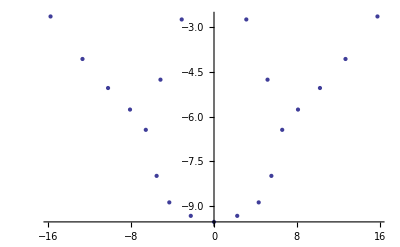

```mathematica
QNM20000016⟦2⟧
ListPlot[Transpose[{Re[%],Im[%]}]]
```

```mathematica
QNM40000016=QNM[40,0,0,16];
```

{32.96618641-4.655464387 ⅈ,-32.96618631-4.655464403 ⅈ,-29.01075625-6.415899685 ⅈ,29.01075612-6.415899524 ⅈ,25.7911223-7.696841866 ⅈ,-25.79112216-7.696841872 ⅈ,-22.97285032-8.72371073 ⅈ,22.9728499-8.723711404 ⅈ,20.42795387-9.582772268 ⅈ,-20.42795357-9.582772692 ⅈ,-18.08897132-10.31901403 ⅈ,18.08897133-10.319014 ⅈ,-10.16831888-17.26342933 ⅈ,10.16830862-17.26342888 ⅈ,-15.91301272-10.96021262 ⅈ,15.9130127-10.96021262 ⅈ,9.184295345-15.82372111 ⅈ,-9.184275994-15.82371071 ⅈ,-6.961499319-16.84255397 ⅈ,6.961495889-16.84253168 ⅈ,4.711357381-17.42735313 ⅈ,-4.711365386-17.4273337 ⅈ,13.87995348-11.51261097 ⅈ,-13.87995339-11.51261085 ⅈ,-2.378514464-17.78526058 ⅈ,2.378531327-17.78524909 ⅈ,-0.00001009683746-17.90706542 ⅈ,-10.84800961-14.04321873 ⅈ,10.84800449-14.04322085 ⅈ,-12.20348555-12.32340795 ⅈ,12.20348621-12.32340703 ⅈ,-11.2069283-10.77628279 ⅈ,11.20692826-10.77628269 ⅈ,-9.197199544-8.772480261 ⅈ,9.197199539-8.772480265 ⅈ,-7.187930829-6.769564911 ⅈ,7.18793081-6.769564914 ⅈ,5.169521018-4.763570133 ⅈ,-5.169520953-4.763570145 ⅈ,-3.1194516-2.746675748 ⅈ,3.119451591-2.746675744 ⅈ}

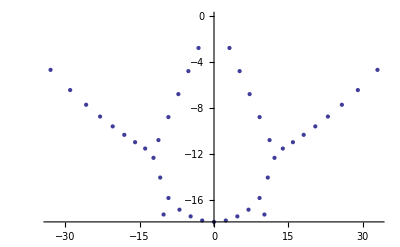

```mathematica
QNM40000016⟦2⟧
ListPlot[Transpose[{Re[%],Im[%]}]]
```

### Convergence

### Analysis of the eigenfunctions

## Spin 1

### Not needed

```mathematica
spin1={1,2,V1,V2,13,23,R1,R2};
nameSpin1=Table[ToExpression["eqn"<>ToString[spin1⟦i⟧]],{i,Length[spin1]}];

listSpin1={maxFR⟦2⟧,maxFR⟦3⟧,ensFR⟦1,2⟧,ensFR⟦1,3⟧,ensFR⟦4,2⟧,ensFR⟦4,3⟧,ensFR⟦5,2⟧,ensFR⟦5,3⟧};
nameSpin1=listSpin1;
```

```mathematica
nameSpin1⟦1⟧
```

-1/r^4(r^3 (-k^2+ⅈ r ω) a1[r]-2 √3 q r hV1[r]-3 q^2 a1'[r]+m r^2 a1'[r]+3 r^6 a1'[r]+2 ⅈ r^5 ω a1'[r]+√3 q r^2 hV1'[r]+q^2 r a1''[r]-m r^3 a1''[r]+r^7 a1''[r])

### List of equation

```mathematica
varSpin1={a1,a2,hV1,hV2,h13,h23};
eqnSpin1={maxFR⟦2⟧,maxFR⟦3⟧,ensFR⟦1,2⟧,ensFR⟦1,3⟧,ensFR⟦4,2⟧,ensFR⟦4,3⟧,ensFR⟦5,2⟧,ensFR⟦5,3⟧};
```

```mathematica
dksdsk={aa,cc,xx,ddd,xx,zz}
```

{aa,cc,xx,ddd,xx,zz}

```mathematica
Table[varSpin1⟦i⟧->(#^Subscript[α, i] dksdsk⟦i⟧[1/#]&),{i,Length[varSpin1]}]->Table[(#^Subscript[α, i] dksdsk⟦i⟧[1/#]&),{i,Length[varSpin1]}]
```

{a1→(#1^α_i dksdsk⟦i⟧[1/#1]&),a2→(#1^α_i dksdsk⟦i⟧[1/#1]&),hV1→(#1^α_i dksdsk⟦i⟧[1/#1]&),hV2→(#1^α_i dksdsk⟦i⟧[1/#1]&),h13→(#1^α_i dksdsk⟦i⟧[1/#1]&),h23→(#1^α_i dksdsk⟦i⟧[1/#1]&)}→{#1^α_i dksdsk⟦i⟧[1/#1]&,#1^α_i dksdsk⟦i⟧[1/#1]&,#1^α_i dksdsk⟦i⟧[1/#1]&,#1^α_i dksdsk⟦i⟧[1/#1]&,#1^α_i dksdsk⟦i⟧[1/#1]&,#1^α_i dksdsk⟦i⟧[1/#1]&}

```mathematica
Table[varSpin1⟦i⟧->(#^Subscript[α, i] dksdsk⟦i⟧[1/#]&),{i,Length[varSpin1]}]
Subscript[ff, i]->(1+O[#]&)
```

{a1→(#1^α_i dksdsk⟦i⟧[1/#1]&),a2→(#1^α_i dksdsk⟦i⟧[1/#1]&),hV1→(#1^α_i dksdsk⟦i⟧[1/#1]&),hV2→(#1^α_i dksdsk⟦i⟧[1/#1]&),h13→(#1^α_i dksdsk⟦i⟧[1/#1]&),h23→(#1^α_i dksdsk⟦i⟧[1/#1]&)}

ff_i→(1+O[#1]&)

```mathematica
exponents={γ1->2,γ2->2,γ3->2,γ4->2, γ5->2,γ6->2};
boundarySeries={ϕvx->(#^-γ1 φvx[1/#]&),ϕvy->(#^-γ2 φvy[1/#]&),ϕxz->(#^-γ3 φxz[1/#]&),ϕyz->(#^-γ4 φyz[1/#]&),αx->(#^-γ5 ax[1/#]&),αy->(#^-γ6 ay[1/#]&)};
boundaryLeading={φvx->(1+O[#]&),φxz->(1+O[#]&),ax->(1+O[#]&),φvy->(1+O[#]&),φyz->(1+O[#]&),ay->(1+O[#]&)};
```

```mathematica
ff_[r_]-> u^-γ ff[1/r]
```

```mathematica
uI
```

```mathematica
Table[listSpin1[[i]]/.r->1/u/.ff_[uI_]->uI^-γ ff[1/uI]/.fff_[u]->(1+O[u])//Simplify,{i,Length[listSpin1]}];
Normal[%]
```

{-(1/u)^(3-γ),-(1/u)^(3-γ),-1/2 (1/u)^(2-γ),-1/2 (1/u)^(2-γ),-1/2 (1/u)^(2-γ),-1/2 (1/u)^(2-γ),-1/2 (1/u)^-γ,-1/2 (1/u)^-γ}

```mathematica
listSpin1⟦1⟧/.r->1/u/.ruleBD1;
%/.ruleBD2//Simplify;
%/.ruleNO1
```

## Spin 0

```mathematica
spin0={V,3,R,VV,V3,VR,33,R3,RR,DD};
nameSpin0=Table[ToExpression["eqn"<>ToString[spin0⟦i⟧]],{i,Length[spin0]}];

listSpin0={maxFR⟦1⟧,maxFR⟦4⟧,maxFR⟦5⟧,ensFR⟦1,1⟧,ensFR⟦1,4⟧,ensFR⟦1,5⟧,ensFR⟦4,4⟧,ensFR⟦5,4⟧,ensFR⟦5,5⟧,ensFR⟦2,2⟧+ensFR⟦3,3⟧/.h11-> Function[z,hDD[z]-h22[z]]//Simplify};
nameSpin0=listSpin0; (* there is issue in the trace term here. *)
```

```mathematica
nameSpin0//MatrixForm
```

((-2 √3 q h11[r]-2 √3 q h22[r]-2 √3 q h33[r]-2 ⅈ k r^4 a3'[r]+6 r^5 aV'[r]+√3 q r h11'[r]+√3 q r h22'[r]+√3 q r h33'[r]+2 r^6 aV''[r])/(2 r^3)
-(ⅈ r^4 ω a3[r]+ⅈ k r^4 aV[r]-2 √3 q r hV3[r]-3 q^2 a3'[r]+m r^2 a3'[r]+3 r^6 a3'[r]+2 ⅈ r^5 ω a3'[r]+ⅈ k r^5 aV'[r]+√3 q r^2 hV3'[r]+q^2 r a3''[r]-m r^3 a3''[r]+r^7 a3''[r])/r^4
(ⅈ (2 ⅈ k r^4 ω a3[r]+2 ⅈ k^2 r^4 aV[r]+√3 q r ω h11[r]+√3 q r ω h22[r]+√3 q r ω h33[r]+2 √3 k q r hV3[r]+2 k q^2 a3'[r]-2 k m r^2 a3'[r]+2 k r^6 a3'[r]+2 r^6 ω aV'[r]))/(2 r^3)
1/2 ((ⅈ (-2 q^2+m r^2+r^6) ω (h11[r]+h22[r]+h33[r]))/r^7+(ω^2 (h11[r]+h22[r]+h33[r]))/r^2-(-8+(4 q^2)/r^6) hVV[r]+(k (2 ⅈ (-2 q^2+m r^2+r^6-ⅈ r^5 ω) hV3[r]+k r^5 hVV[r]))/r^7+(4 √3 q (√3 q r hVV[r]-2 (q^2-m r^2+r^6) aV'[r]))/r^7+((q^2-m r^2+r^6) (-2 q^2+m r^2+r^6) (-2 h11[r]-2 h22[r]-2 h33[r]+r h11'[r]+r h22'[r]+r h33'[r]))/r^12+(4 (-2 q^2+m r^2+r^6) hVV'[r])/r^5-ⅈ ω hVV'[r]-(3 ((-4 q^2+2 m r^2+2 r^6-ⅈ r^5 ω) hVV[r]+r (q^2-m r^2+r^6) hVV'[r]))/r^6-((q^2-m r^2+r^6) ((6 q^2-r^2 (2 m+k^2 r^2+6 r^4)) h11[r]+(6 q^2-2 m r^2-k^2 r^4-6 r^6) h22[r]+6 q^2 h33[r]-2 m r^2 h33[r]-6 r^6 h33[r]+4 ⅈ k r^5 hV3[r]-6 r^6 hVV[r]-4 √3 q r^5 aV'[r]-4 q^2 r h11'[r]+2 m r^3 h11'[r]+2 r^7 h11'[r]+2 ⅈ r^6 ω h11'[r]-4 q^2 r h22'[r]+2 m r^3 h22'[r]+2 r^7 h22'[r]+2 ⅈ r^6 ω h22'[r]-4 q^2 r h33'[r]+2 m r^3 h33'[r]+2 r^7 h33'[r]+2 ⅈ r^6 ω h33'[r]+2 ⅈ k r^6 hV3'[r]-6 r^7 hVV'[r]+q^2 r^2 h11''[r]-m r^4 h11''[r]+r^8 h11''[r]+q^2 r^2 h22''[r]-m r^4 h22''[r]+r^8 h22''[r]+q^2 r^2 h33''[r]-m r^4 h33''[r]+r^8 h33''[r]-r^8 hVV''[r]))/r^12-(2 (10 q^2-3 m r^2+r^6) hVV[r]+r ((-8 q^2+4 m r^2+4 r^6-ⅈ r^5 ω) hVV'[r]+r (q^2-m r^2+r^6) hVV''[r]))/r^6)
2 (2-q^2/r^6) hV3[r]-(2 √3 q (ⅈ ω a3[r]+ⅈ k aV[r]+((q^2-m r^2+r^6) a3'[r])/r^4))/r^3-(4 (-2 q^2+m r^2+r^6) hV3[r]+r ((q^2-m r^2+r^6) hV3'[r]+r^3 (k ω h11[r]+ⅈ (-ⅈ k ω h22[r]+r (-2 ω hV3[r]+k hVV[r]+r ω hV3'[r]+k r hVV'[r])))+r (q^2-m r^2+r^6) hV3''[r]))/(2 r^6)
-((2 q^2-r^4 (k^2+4 r^2-ⅈ r ω)) h11[r]+(2 q^2-r^4 (k^2+4 r^2-ⅈ r ω)) h22[r]+2 q^2 h33[r]-4 r^6 h33[r]+ⅈ r^5 ω h33[r]+4 ⅈ k r^5 hV3[r]-6 r^6 hVV[r]+4 √3 q r^5 aV'[r]-2 q^2 r h11'[r]+m r^3 h11'[r]+r^7 h11'[r]+ⅈ r^6 ω h11'[r]-2 q^2 r h22'[r]+m r^3 h22'[r]+r^7 h22'[r]+ⅈ r^6 ω h22'[r]-2 q^2 r h33'[r]+m r^3 h33'[r]+r^7 h33'[r]+ⅈ r^6 ω h33'[r]+ⅈ k r^6 hV3'[r]-3 r^7 hVV'[r]+q^2 r^2 h11''[r]-m r^4 h11''[r]+r^8 h11''[r]+q^2 r^2 h22''[r]-m r^4 h22''[r]+r^8 h22''[r]+q^2 r^2 h33''[r]-m r^4 h33''[r]+r^8 h33''[r])/(2 r^8)
((8 q^2-4 m r^2-4 r^6-ⅈ r^5 ω) h11[r]+(8 q^2-4 m r^2-4 r^6-ⅈ r^5 ω) h22[r]+r (-2 r^5 hVV[r]-4 √3 q r^4 aV'[r]-5 q^2 h11'[r]+3 m r^2 h11'[r]+r^6 h11'[r]+2 ⅈ r^5 ω h11'[r]-5 q^2 h22'[r]+3 m r^2 h22'[r]+r^6 h22'[r]+2 ⅈ r^5 ω h22'[r]-4 r^6 hVV'[r]+q^2 r h11''[r]-m r^3 h11''[r]+r^7 h11''[r]+q^2 r h22''[r]-m r^3 h22''[r]+r^7 h22''[r]-r^7 hVV''[r]))/(2 r^6)
-(-2 ⅈ k h11[r]-2 ⅈ k h22[r]-4 r hV3[r]+4 √3 q a3'[r]+ⅈ k r h11'[r]+ⅈ k r h22'[r]+r^2 hV3'[r]+r^3 hV3''[r])/(2 r^3)
-(2 h11[r]+2 h22[r]+2 h33[r]-2 r h11'[r]-2 r h22'[r]-2 r h33'[r]+r^2 h11''[r]+r^2 h22''[r]+r^2 h33''[r])/(2 r^4)
(2 (8 q^2-4 m r^2-4 r^6-ⅈ r^5 ω) h33[r]+(8 q^2-r^2 (4 m+r^2 (k^2+4 r^2+ⅈ r ω))) hDD[r]+r (4 ⅈ k r^4 hV3[r]-4 r^5 hVV[r]-8 √3 q r^4 aV'[r]-10 q^2 h33'[r]+6 m r^2 h33'[r]+2 r^6 h33'[r]+4 ⅈ r^5 ω h33'[r]-5 q^2 hDD'[r]+3 m r^2 hDD'[r]+r^6 hDD'[r]+2 ⅈ r^5 ω hDD'[r]+4 ⅈ k r^5 hV3'[r]-8 r^6 hVV'[r]+2 q^2 r h33''[r]-2 m r^3 h33''[r]+2 r^7 h33''[r]+q^2 r hDD''[r]-m r^3 hDD''[r]+r^7 hDD''[r]-2 r^7 hVV''[r]))/(2 r^6))